## Solving with knowns: mdot, α, constant κR

```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
dirName="/home/dan/ResearchLocal/"
SetDirectory[dirName];
```

/home/dan/ResearchLocal/

```mathematica
eqTab={
ν==α cs h,
cs^2==(kb Tc)/(μ mp),
ρ==1/(√(2 π))Σ/h,
h==cs/Ω,
Tc^4==3/4 τ Tdisk^4,
τ==1/2 Σ κR,
ν Σ==mdot/(3π),
σ Tdisk^4==9/8 ν Σ Ω^2,
κR==κR0(*,
β==ρ cs^2/B^2,
α==b1*β^-b2*)
};
Length[eqTab]
```

9

```mathematica
unknowns=ToString[{Tc, Tdisk, cs, ρ, h,κR, ν, τ,Σ(*, β,α*)}];
knownsFuncs={Ω};
constants={kb, μ, mp, G, M,σ,mdot};
```

```mathematica
rulesTab={ν>0,α>0,cs>0,h>0,kb>0,Tc>0,μ>0,mp>0,ρ>0,Σ>0,Ω>0,τ>0,Tdisk>0,τ>0,mdot>0,σ>0,κR>0,κR0>0,Tc>0(*,β>0,B>0,b1>0,b2>0*)};
```

```mathematica
sol1=Solve[Flatten[{eqTab,rulesTab}],{Tc, Tdisk, cs, ρ, h,κR, ν, τ,Σ(*, β,α*)},Reals];
```

```mathematica
sol2=Reduce[Flatten[{eqTab,rulesTab}],{Tc, Tdisk, cs, ρ, h,κR, ν, τ,Σ(*, β,α*)},Reals];
```

```mathematica
sol2Tab=Table[sol2[[i]],{i,1,17}]//TableForm
```

Ω>0
σ>0
μ>0
κR0>0
α>0
mp>0
mdot>0
kb>0
Tc==Root[-3 mdot^2 mp κR0 μ Ω^3+64 kb π^2 α σ #1^5&,1]
Tdisk==Root[-8 kb π Tc^5 α+mdot mp κR0 μ Ω #1^4&,2]
cs==(√((mdot Tdisk^4 κR0 Ω)/(Tc^4 α)))/(2 √(2 π))
ρ==(mdot Ω^2)/(3 √2 cs^3 π^(3/2) α)
h==cs/Ω
κR==(4 √(2/π) Tc^4)/(3 h Tdisk^4 ρ)
ν==cs h α
τ==(4 Tc^4)/(3 Tdisk^4)
Σ==h √(2 π) ρ

```mathematica
mp=1;μ=1;kb=1;mdot=1;κR0=1;mp=1;σ=1;α=0.01;
```

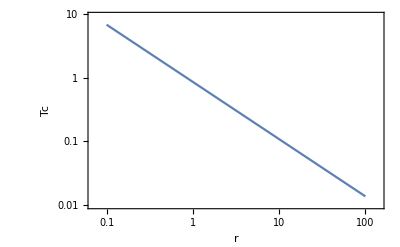
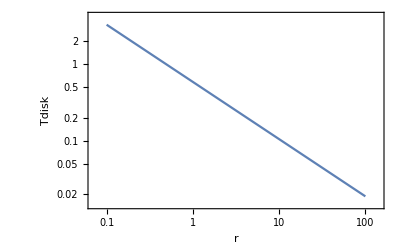
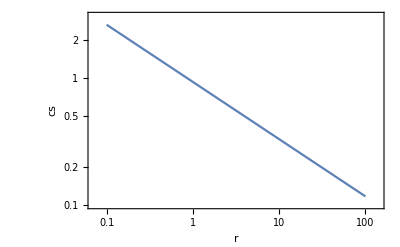
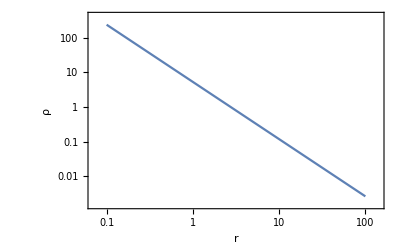
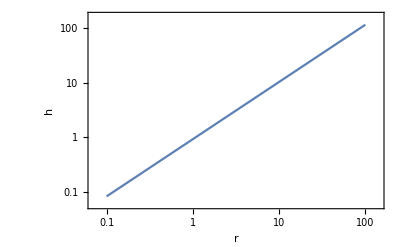
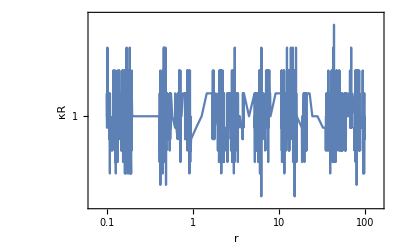
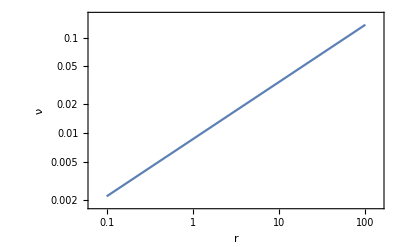
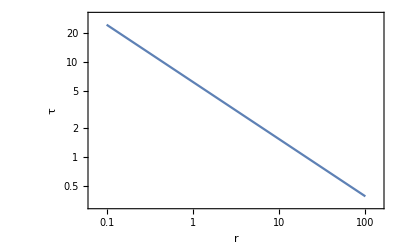
-Graphics- | -9/10
-Graphics- | -3/4
-Graphics- | -9/20
-Graphics- | -33/20
-Graphics- | 21/20
-Graphics- | 9.64327×10^-17
-Graphics- | 3/5
-Graphics- | -3/5
-Graphics- | -3/5

```mathematica
Table[
{LogLogPlot[sol1[[1,i,2,1]]/.{Ω->r^(-3/2)},{r,0.1,100},Frame->True,FrameLabel->{"r",sol1[[1,i,1]]}],
Log10[(sol1[[1,i,2,1]]/.{Ω->r^(-3/2)}/.{r->10})/(sol1[[1,i,2,1]]/.{Ω->r^(-3/2)}/.{r->1})]//Rationalize}
,{i,1,9}]//TableForm
```

## Solving with knowns: mdot, α, constant κR

```mathematica
$HistoryLength=0;ClearAll["Global`*"]; 
dirName="/home/dan/ResearchLocal/"
SetDirectory[dirName];
```

/home/dan/ResearchLocal/

```mathematica
eqTab={
ν==α cs h,
cs^2==(kb Tc)/(μ mp),
ρ==1/(√(2 π))Σ/h,
h==cs/Ω,
Tc^4==3/4 τ Tdisk^4,
τ==1/2 Σ κR,
ν Σ==mdot/(3π),
σ Tdisk^4==9/8 ν Σ Ω^2,
κR==κR0,
β==ρ cs^2/B^2,
α==b1*β^-b2
};
Length[eqTab]
```

11

```mathematica
b1=11;b2=0.53;
```

```mathematica
unknowns=ToString[{Tc, Tdisk, cs, ρ, h,κR, ν, τ,Σ, β,α}];
knownsFuncs={Ω};
constants={kb, μ, mp, G, M,σ,mdot};
```

```mathematica
rulesTab={ν>0,α>0,cs>0,h>0,kb>0,Tc>0,μ>0,mp>0,ρ>0,Σ>0,Ω>0,τ>0,Tdisk>0,τ>0,mdot>0,σ>0,κR>0,κR0>0,Tc>0,β>0,B>0,b1>0,b2>0};
```

```mathematica
(*sol1=Solve[Flatten[{eqTab,rulesTab}],{Tc, Tdisk, cs, ρ, h,κR, ν, τ,Σ, β,α},Reals];*)
```

```mathematica
sol2=Reduce[Flatten[{eqTab,rulesTab}],{Tc, Tdisk, cs, ρ, h,κR, ν, τ,Σ, β,α},Reals];
```

$Aborted

```mathematica
sol2Tab=Table[sol2[[i]],{i,1,17}]//TableForm
```

Ω>0
σ>0
μ>0
κR0>0
mp>0
mdot>0
kb>0
Tc>0
Tdisk==Root[-3 mdot Ω^2+8 π σ #1^4&,2]
cs==√((kb Tc)/(mp μ))
ρ==(4 √(2/π) Tc^4 Ω)/(3 cs Tdisk^4 κR0)
h==cs/Ω
κR==(4 √(2/π) Tc^4)/(3 h Tdisk^4 ρ)
ν==mdot/(3 √2 h π^(3/2) ρ)
τ==(4 Tc^4)/(3 Tdisk^4)
Σ==h √(2 π) ρ
α==ν/(cs h)

```mathematica
mp=1;μ=1;kb=1;mdot=1;κR0=1;mp=1;σ=1;α=0.01;
```

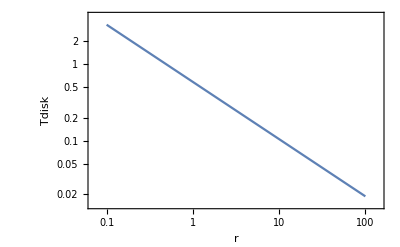
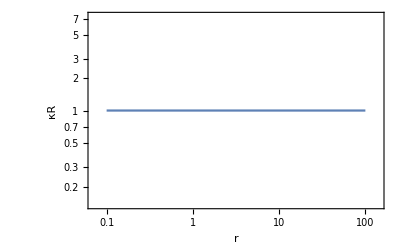
-Graphics- | -3
-Graphics- | -3/4
-Graphics- | Log[1/(10 √10)]/Log[10]
-Graphics- | -9
-Graphics- | 0
-Graphics- | 9
-Graphics- | -9
-Graphics- | -9
-Graphics- | Log[10000000000 √10]/Log[10]

```mathematica
Table[
{LogLogPlot[sol1[[1,i,2,1]]/.{Ω->r^(-3/2)},{r,0.1,100},Frame->True,FrameLabel->{"r",sol1[[1,i,1]]}],
Log10[(sol1[[1,i,2,1]]/.{Ω->r^(-3/2),B->r^(-1/2)}/.{r->10})/(sol1[[1,i,2,1]]/.{Ω->r^(-3/2),B->r^(-1/2)}/.{r->1})]//Rationalize}
,{i,1,9}]//TableForm
```